```mathematica
fy[x_] = (r2-(x-x0)^2)^(0.5)+y0
fyn[x_] = -(r2-(x-x0)^2)^(0.5)+y0
Solve[y1==fy[x1]&&r2>0,{y0},Reals]
```

(r2-(x-x0)^2)^0.5+y0

-(r2-(x-x0)^2)^0.5+y0

{{y0→ConditionalExpression[-1. √(r2-1. (-1. x0+x1)^2)+y1,r2>x0^2-2. x0 x1+x1^2]}}

```mathematica
Solve[y1==fy[x1]&&y2==fy[x2]&&y3==fy[x3]&&r2>0,{y0},Reals]
```

```mathematica
Solve[y1==fy[x1]&&y2==fy[x2]&&y3==fy[x3]&&r2>0,{y0},Reals]
```

```mathematica
Solve[(x1-x0)^2-(x2-x0)^2 == (y2-y0)^2-(y1-y0)^2 , x0]
```

{{x0→(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))}}

```mathematica
y0[x1_,y1_,x2_,y2_,x3_,y3_] = ((y3^2-y1^2-x1^2+x3^2)(x1-x2)+(x3-x1)(y2^2-y1^2-x1^2+x2^2))/(2*((y2-y1)(x3-x1)-(y3-y1)(x2-x1)))
```

((-x1+x3) (-x1^2+x2^2-y1^2+y2^2)+(x1-x2) (-x1^2+x3^2-y1^2+y3^2))/(2 ((-x1+x3) (-y1+y2)-(-x1+x2) (-y1+y3)))

```mathematica
x0[x1_,y1_,x2_,y2_] =(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))
```

(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))

```mathematica
r2[x1_,y1_] = (x1-x0)^2+(y1-y0)^2
```

(-x0+x1)^2+(-y0+y1)^2

```mathematica
y0[-1,0,1,0,1,0]
x0[-1,0,0,1]/.{y0->y0[-1,0,1,0,1,0]}
r2 [-1,0]/.{x0->x0[-1,0,0,1]/.{y0->y0[-1,0,1,0,1,0]},y0->y0[-1,0,1,0,1,0]}
```

0

0

1

```mathematica
pts = {{0,0},{1,3},{-2,3}}
```

{{0,0},{1,3},{-2,3}}

```mathematica
yob=y0[pts[[1]][[1]],pts[[1]][[2]],pts[[2]][[1]],pts[[2]][[2]],pts[[3]][[1]],pts[[3]][[2]]]
xob=x0[pts[[1]][[1]],pts[[1]][[2]],pts[[2]][[1]],pts[[2]][[2]]]/.{y0->yob}
r2b=r2 [pts[[1]][[1]],pts[[1]][[2]]]/.{x0->xob,y0->yob}
```

11/6

-1/2

65/18

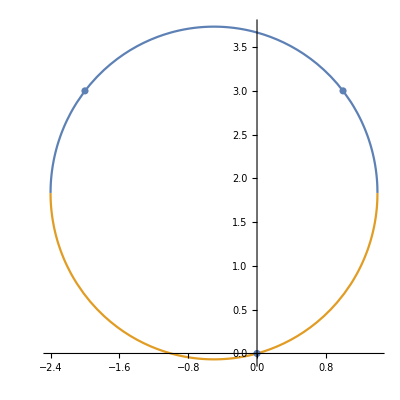

```mathematica
Show[Plot[{fy[x]/.{y0->yob, x0->xob,r2->r2b},fyn[x]/.{y0->yob, x0->xob,r2->r2b}},{x,xob-Sqrt[r2b],xob+Sqrt[r2b]},AspectRatio->1,PlotRange->{{xob-Sqrt[r2b],xob+Sqrt[r2b]},{yob-Sqrt[r2b],yob+Sqrt[r2b]}}],ListPlot[pts]]
```